```mathematica
(*F = ma sprendinys*)
Clear[F,m,c]
(*Solve the differential equation*)
sol1=DSolve[{z''[t]==F/m*Sqrt[(1-(t*z''[t]/c)^2)],z[0]==0,z'[0]==0},z[t],t]
sol1a = DSolve[{z''[t]==F/m*Sqrt[(1-(z'[t]/c)^2)],z[0]==0,z'[0]==0},z[t],t]
D[D[sol1[[2]],t],t]
```

{{z[t]→-(c (√(c^2 m^2)-√(c^2 m^2+F^2 t^2)+F t ArcTanh[(F t)/(√(c^2 m^2+F^2 t^2))]))/F},{z[t]→(c (√(c^2 m^2)-√(c^2 m^2+F^2 t^2)+F t ArcTanh[(F t)/(√(c^2 m^2+F^2 t^2))]))/F}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z[t]→(-c^2 m+c^2 m Cos[(F t)/(c m)])/F},{z[t]→(c^2 m+c^2 m Cos[(-c m π+F t)/(c m)])/F}}

{z''[t]→(c ((F^4 t^2)/((c^2 m^2+F^2 t^2)^(3/2))-F^2/(√(c^2 m^2+F^2 t^2))+(F t ((3 F^5 t^3)/((c^2 m^2+F^2 t^2)^(5/2))-(3 F^3 t)/((c^2 m^2+F^2 t^2)^(3/2))))/(1-(F^2 t^2)/(c^2 m^2+F^2 t^2))-(F t ((2 F^4 t^3)/((c^2 m^2+F^2 t^2)^2)-(2 F^2 t)/(c^2 m^2+F^2 t^2)) (-(F^3 t^2)/((c^2 m^2+F^2 t^2)^(3/2))+F/(√(c^2 m^2+F^2 t^2))))/((1-(F^2 t^2)/(c^2 m^2+F^2 t^2))^2)+(2 F (-(F^3 t^2)/((c^2 m^2+F^2 t^2)^(3/2))+F/(√(c^2 m^2+F^2 t^2))))/(1-(F^2 t^2)/(c^2 m^2+F^2 t^2))))/F}

```mathematica
(*Define the parameters*)
(*F=10; (*Force*)*)
m=0.005; (*Mass*)
c=3*10^8; (*Speed of light*)
```

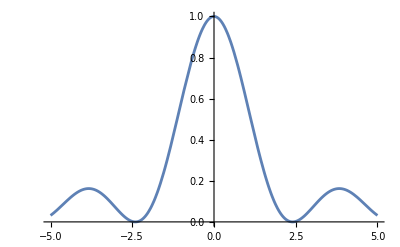

```mathematica
Plot[Abs[BesselJ[0,x]]^2,{x,-5,5}]
```

```mathematica
(*Duoda atstumą iki pirmo nulio*)
N[BesselJZero[0,1]]
```

2.40483

```mathematica
(* Burės paviršiaus plotas () *)
Sail=2*Pi*Integrate[x,{x,0,N[BesselJZero[0,1]]}]
```

18.1684

```mathematica
(*Intensyvumo funkcija paveikta x operatoriumi ir suintegruota.
Gaunasi vidutinė intensyvumo reikšmė per visą paviršių*)
Beselis=2*Pi*Integrate[x*Abs[BesselJ[0,x]]^2,{x,0,N[BesselJZero[0,1]]}]
```

4.89664

```mathematica
Clear[F]
P = 1000000; (*Beam overall power*)
(*Force acting on sail*)
F = 4*Pi*P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, N[BesselJZero[0,1]]}]
```

0.0326443

```mathematica
(*Extract the solution function*)
zSol[t_]=z[t]/. sol1[[2]];
(*Plot the solution*)
Manipulate[Plot[zSol[t],{t,0,tMax},PlotRange->{{0,tMax},Automatic},AxesLabel->{"t","z(t)"},PlotLabel->"Solution to the Differential Equation",GridLines->Automatic],
{{tMax,10,"Maximum Time"},1,1000,1}
]
```

```mathematica
(*Define the parameters*)
m= 0.01; (*mass*)
c=3*10^8; (*speed of light*)
w0=1; (*waist radius*)
n=1; (*refraction index*)
lam=600*10^-9; (*wavelength*)
P=100000000000; (*Bessel beam overall power*)
gRadius[z_]:=w0*Sqrt[1+(z^2)/Zr^2]; (*Gauss radius*)
Zr=N[Pi]*w0^2*n/lam; (*Rayleigh range*)
radius = 1;
```

```mathematica
(*Bessel part*)
I0 = 2*P/N[Pi]/w0^2; (*Beam overall power*)
(*Force acting on sail*)
F = P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, w0}]
```

500/3 (BesselJ[0,1]^2+BesselJ[1,1]^2)

```mathematica
(*Define the ODE with the new gIntensity[z[t]]*)
gIntensity[z_]:=I0/c*(w0/gRadius[z])^2*Exp[-2*r^2/gRadius[z]^2];
eqn=z''[t]*m/Sqrt[(1-(t*z''[t]/c)^2)]==Integrate[gIntensity[z[t]],{r,0,w0}];
```

```mathematica
(*Define the initial conditions*)
initialConditions={z'[0]==0,z[0]==0};
```

```mathematica
(*Solve the ODE numerically*)
Tmax=100; (*You can adjust this based on your problem*)
sol=NDSolve[{eqn,initialConditions},z,{t,0,Tmax}];
sol = sol[[2]]
```

{z→InterpolatingFunction[…]}

```mathematica
D[D[z[t]/. sol1[[2]],t],t]
```

1/(BesselJ[0,1]^2+BesselJ[1,1]^2)1800000 ((62500000000 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^4)/(81 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)^(3/2))-(250000 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)/(9 √(9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2))+(500 t (BesselJ[0,1]^2+BesselJ[1,1]^2) ((31250000000000 t^3 (BesselJ[0,1]^2+BesselJ[1,1]^2)^5)/(81 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)^(5/2))-(125000000 t (BesselJ[0,1]^2+BesselJ[1,1]^2)^3)/(9 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)^(3/2))))/(3 (1-(250000 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)/(9 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2))))-(500 t (BesselJ[0,1]^2+BesselJ[1,1]^2) ((125000000000 t^3 (BesselJ[0,1]^2+BesselJ[1,1]^2)^4)/(81 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)^2)-(500000 t (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)/(9 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2))) (-(125000000 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^3)/(27 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)^(3/2))+(500 (BesselJ[0,1]^2+BesselJ[1,1]^2))/(3 √(9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2))))/(3 (1-(250000 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)/(9 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)))^2)+(1000 (BesselJ[0,1]^2+BesselJ[1,1]^2) (-(125000000 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^3)/(27 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)^(3/2))+(500 (BesselJ[0,1]^2+BesselJ[1,1]^2))/(3 √(9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2))))/(3 (1-(250000 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)/(9 (9.×10^12+250000/9 t^2 (BesselJ[0,1]^2+BesselJ[1,1]^2)^2)))))

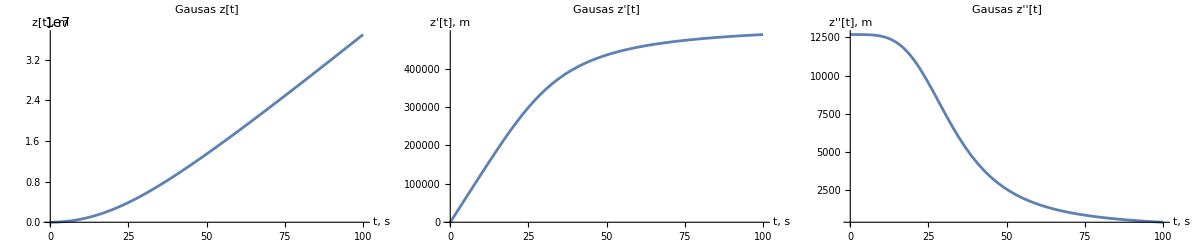

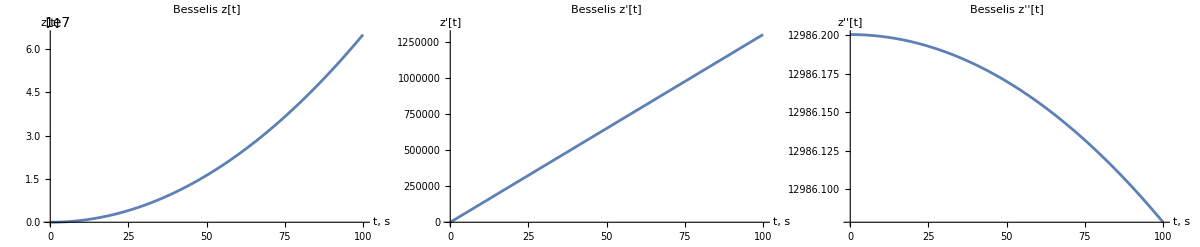

```mathematica
plot1=Plot[Evaluate[z[t]/. sol],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z[t], m"},PlotLabel->"Gausas z[t]"];

plot2=Plot[Evaluate[Derivative[1][z][t]/. sol],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z'[t], m"},PlotLabel->"Gausas z'[t]"];

plot3=Plot[Evaluate[Derivative[2][z][t]/. sol],{t,0.0001,Tmax},PlotRange->All,AxesLabel->{"t, s","z''[t], m"},PlotLabel->"Gausas z''[t]"]; 

plot4=Plot[Evaluate[z[t]/. sol1[[2]]],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z[t]"},PlotLabel->"Besselis z[t]"];
plot5=Plot[Evaluate[D[z[t]/. sol1[[2]],t]],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z'[t]"},PlotLabel->"Besselis z'[t]"];
plot6=Plot[Evaluate[D[D[z[t]/.sol1[[2]],t],t]],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z''[t]"},PlotLabel->"Besselis z''[t]"];

GraphicsGrid[{{plot1,plot2,plot3}},Spacings->{0,0},ImageSize->Full]
GraphicsGrid[{{plot4,plot5,plot6}},Spacings->{0,0},ImageSize->Full]
plot1;
plot4;
```